# Define functions for MAD data

### Extract the coordinates: X,Y,Z

```mathematica
Clear[GetXYZ];
GetXYZ[x_]:=Module[
{f},
f[y_]:={y[[4]],y[[5]],y[[6]],y[[3]]};
f/@x
]
```

### Extract the coordinates: X,Y

```mathematica
Clear[GetXY];
GetXY[x_]:=Module[
{f},
f[y_]:={y[[4]],y[[5]]};
f/@x
]
```

### Generate: length, height

```mathematica
Clear[CalculateLH];
CalculateLH[x_]:=Module[
{f},
f[y_]:={√((y[[1]]-1880.1405971)^2+(y[[2]]-2090.7822669)^2),y[[3]]-2433.66};
f/@x
]
```

# Get TFS fileBT. Output from 2007: BT_BEAM_COORDINATES.csv BTP_BEAM_COORDINATES.csv

```mathematica
fileBT=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/out/BT1.survey","Table"];
fileBTP=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/out/BTP.survey","Table"];
fileBT1BTP=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/out/BT1_BTP.survey","Table"];
fileBT2BTP=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/out/BT2_BTP.survey","Table"];
fileBT3BTP=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/out/BT3_BTP.survey","Table"];
fileBT4BTP=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/out/BT4_BTP.survey","Table"];
```

```mathematica
fileBT[[Range[1,27+4+23]]]
```

{{@,NAME,%06s,SURVEY},{@,TYPE,%06s,SURVEY},{@,TITLE,%42s,Transferline BT1 optics. Protons - 1.4 GeV},{@,ORIGIN,%22s,MAD-X 5.02.01 Linux 64},{@,DATE,%08s,22/05/14},{@,TIME,%08s,13.10.57},{*,NAME,S,L,Z,X,Y},{$,%s,%le,%le,%le,%le,%le},{BT1$START,0.,0.,1880.14,2090.78,2432.94},{BT1.START,0.,0.,1880.14,2090.78,2432.94},{DRIFT_0,2.54897,2.54897,1881.25,2093.08,2432.94},{BT1.BVT10,3.45579,0.906823,1881.64,2093.89,2432.97},{DRIFT_1,3.6107,0.154908,1881.71,2094.03,2432.99},{BT1.BPM00,4.1187,0.508,1881.93,2094.49,2433.03},{DRIFT_2,4.29897,0.180274,1882.01,2094.65,2433.04},{BT1.DHZ10,4.63397,0.335,1882.15,2094.95,2433.07},{DRIFT_3,4.67824,0.044272,1882.17,2094.99,2433.07},{BT1.VVS10,4.77824,0.1,1882.21,2095.08,2433.08},{DRIFT_4,6.37449,1.59625,1882.91,2096.52,2433.2},{BT1.SMV10,7.3713,0.996808,1883.34,2097.41,2433.24},{DRIFT_5,7.47312,0.101815,1883.38,2097.5,2433.24},{BT2.BTV10,7.47312,0.,1883.38,2097.5,2433.24},{DRIFT_6,8.15312,0.680004,1883.68,2098.12,2433.24},{BT.VPG11,8.15312,0.,1883.68,2098.12,2433.24},{DRIFT_7,8.71063,0.557503,1883.92,2098.62,2433.24},{BT2.BPM10,8.89563,0.185,1884.,2098.78,2433.24},{DRIFT_8,9.14013,0.244502,1884.11,2099.01,2433.24},{BT1.QNO10,9.60614,0.466017,1884.31,2099.42,2433.25},{DRIFT_9,10.7542,1.1481,1884.81,2100.46,2433.26},{BT2.VVS30,10.8542,0.1,1884.85,2100.55,2433.26},{DRIFT_10,11.1403,0.286029,1884.98,2100.81,2433.27},{BT1.QNO20,11.6063,0.466028,1885.18,2101.23,2433.27},{DRIFT_11,13.5189,1.91257,1886.01,2102.95,2433.29},{BT.VGP21,13.5189,0.,1886.01,2102.95,2433.29},{BT.VGR21,13.5189,0.,1886.01,2102.95,2433.29},{BT.VPI22,13.5189,0.,1886.01,2102.95,2433.29},{BT.VPI22A,13.5189,0.,1886.01,2102.95,2433.29},{DRIFT_12,13.9434,0.424516,1886.19,2103.33,2433.29},{BT1.KFA10,15.5034,1.56002,1886.87,2104.74,2433.3},{DRIFT_13,15.9109,0.4075,1887.05,2105.1,2433.3},{BT.BTV20,15.9109,0.,1887.05,2105.1,2433.3},{DRIFT_14,16.1673,0.256386,1887.16,2105.33,2433.3},{BT2.BVT20,17.0811,0.913809,1887.56,2106.16,2433.33},{DRIFT_15,17.3725,0.291398,1887.68,2106.42,2433.36},{BT2.BPM20,17.5575,0.185,1887.76,2106.58,2433.37},{DRIFT_16,18.7631,1.20563,1888.29,2107.67,2433.46},{BT2.DVT40,19.0981,0.335,1888.43,2107.97,2433.48},{DRIFT_17,20.0844,0.986272,1888.86,2108.85,2433.56},{BT.VPI23,20.0844,0.,1888.86,2108.85,2433.56},{DRIFT_18,20.3895,0.305109,1888.99,2109.13,2433.58},{BT2.SMV20,21.3864,0.996845,1889.42,2110.02,2433.62},{DRIFT_19,21.4733,0.086936,1889.46,2110.1,2433.62},{BT2.BTV30,21.4733,0.,1889.46,2110.1,2433.62},{DRIFT_20,22.0713,0.598002,1889.72,2110.64,2433.62}}

```mathematica
Length[fileBTP]
```

557

```mathematica
fileBTP[[Range[85,135]]]
```

{{STRAY11,29.8028,0.,1911.9,2146.16,2433.66},{DRIFT_26,29.8228,0.02,1911.91,2146.18,2433.66},{STRAY12,29.8228,0.,1911.91,2146.18,2433.66},{DRIFT_26,29.8428,0.02,1911.92,2146.19,2433.66},{STRAY13,29.8428,0.,1911.92,2146.19,2433.66},{DRIFT_26,29.8628,0.02,1911.93,2146.21,2433.66},{STRAY14,29.8628,0.,1911.93,2146.21,2433.66},{DRIFT_26,29.8828,0.02,1911.95,2146.23,2433.66},{STRAY15,29.8828,0.,1911.95,2146.23,2433.66},{DRIFT_26,29.9028,0.02,1911.96,2146.24,2433.66},{STRAY16,29.9028,0.,1911.96,2146.24,2433.66},{DRIFT_26,29.9228,0.02,1911.97,2146.26,2433.66},{STRAY17,29.9228,0.,1911.97,2146.26,2433.66},{DRIFT_26,29.9428,0.02,1911.98,2146.28,2433.66},{STRAY18,29.9428,0.,1911.98,2146.28,2433.66},{DRIFT_26,29.9628,0.02,1911.99,2146.29,2433.66},{STRAY19,29.9628,0.,1911.99,2146.29,2433.66},{DRIFT_26,29.9828,0.02,1912.,2146.31,2433.66},{STRAY20,29.9828,0.,1912.,2146.31,2433.66},{DRIFT_26,30.0028,0.02,1912.01,2146.33,2433.66},{STRAY21,30.0028,0.,1912.01,2146.33,2433.66},{DRIFT_26,30.0228,0.02,1912.02,2146.34,2433.66},{STRAY22,30.0228,0.,1912.02,2146.34,2433.66},{DRIFT_26,30.0428,0.02,1912.04,2146.36,2433.66},{STRAY23,30.0428,0.,1912.04,2146.36,2433.66},{DRIFT_26,30.0628,0.02,1912.05,2146.38,2433.66},{STRAY24,30.0628,0.,1912.05,2146.38,2433.66},{DRIFT_26,30.0828,0.02,1912.06,2146.39,2433.66},{STRAY25,30.0828,0.,1912.06,2146.39,2433.66},{DRIFT_26,30.1028,0.02,1912.07,2146.41,2433.66},{STRAY26,30.1028,0.,1912.07,2146.41,2433.66},{DRIFT_26,30.1228,0.02,1912.08,2146.42,2433.66},{STRAY27,30.1228,0.,1912.08,2146.42,2433.66},{DRIFT_26,30.1428,0.02,1912.09,2146.44,2433.66},{STRAY28,30.1428,0.,1912.09,2146.44,2433.66},{DRIFT_26,30.1628,0.02,1912.1,2146.46,2433.66},{STRAY29,30.1628,0.,1912.1,2146.46,2433.66},{DRIFT_26,30.1828,0.02,1912.12,2146.47,2433.66},{STRAY30,30.1828,0.,1912.12,2146.47,2433.66},{DRIFT_26,30.2028,0.02,1912.13,2146.49,2433.66},{STRAY31,30.2028,0.,1912.13,2146.49,2433.66},{DRIFT_26,30.2228,0.02,1912.14,2146.51,2433.66},{STRAY32,30.2228,0.,1912.14,2146.51,2433.66},{DRIFT_26,30.2428,0.02,1912.15,2146.52,2433.66},{STRAY33,30.2428,0.,1912.15,2146.52,2433.66},{DRIFT_26,30.2628,0.02,1912.16,2146.54,2433.66},{STRAY34,30.2628,0.,1912.16,2146.54,2433.66},{DRIFT_26,30.2828,0.02,1912.17,2146.56,2433.66},{STRAY35,30.2828,0.,1912.17,2146.56,2433.66},{DRIFT_26,30.3028,0.02,1912.18,2146.57,2433.66},{STRAY36,30.3028,0.,1912.18,2146.57,2433.66}}

```mathematica
Length[fileBT]
```

79

```mathematica
Length[fileBTP]
```

557

```mathematica
XYBT=GetXY[fileBT[[Range[9,78]]]];
XYBTP=GetXY[fileBTP[[Range[11,62]]]];
```

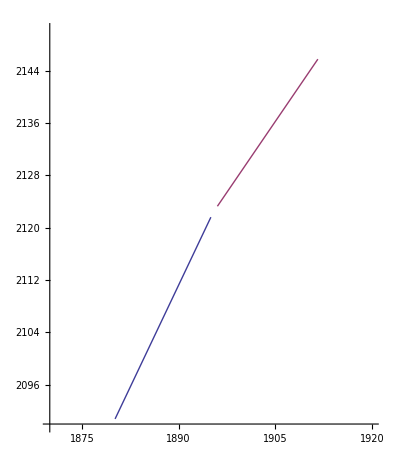

```mathematica
ListLinePlot[{XYBT,XYBTP},PlotRange->{{1870,1920},{2090,2150}},AspectRatio->(2150-2090)/(1920-1870)]
```

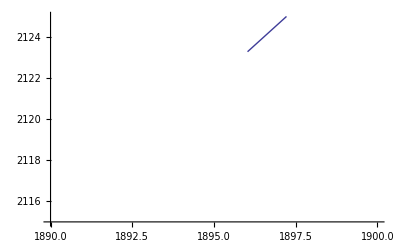

```mathematica
ListLinePlot[{XYBTP},PlotRange->{{1890,1900},{2115,2125}}]
```

```mathematica
XYBT[[18]]
XYBT[[19]]
(XYBT[[18]]+XYBT[[19]])/2
```

{1884.,2098.78}

{1884.11,2099.01}

{1884.05,2098.89}

```mathematica
XYBT[[18+4]]
XYBT[[19+4]]
(XYBT[[18+4]]+XYBT[[19+4]])/2
```

{1884.85,2100.55}

{1884.98,2100.81}

{1884.91,2100.68}

```mathematica
XYBT[[18+4+23]]
XYBT[[19+4+23]]
(XYBT[[18+4+23]]+XYBT[[19+4+23]])/2
```

{1889.46,2110.1}

{1889.72,2110.64}

{1889.59,2110.37}

# Calculate equations for the straight lines

## BT line - before BHZ10

```mathematica
Clear[x];
fileBT[[Range[9,78]]]
XY=GetXY[fileBT[[Range[9,78]]]];
BTlineBeforeBHZ10=LinearModelFit[XY,x,x]
```

{{BT1$START,0.,0.,1880.14,2090.78,2432.94},{BT1.START,0.,0.,1880.14,2090.78,2432.94},{DRIFT_0,2.54897,2.54897,1881.25,2093.08,2432.94},{BT1.BVT10,3.45579,0.906823,1881.64,2093.89,2432.97},{DRIFT_1,3.6107,0.154908,1881.71,2094.03,2432.99},{BT1.BPM00,4.1187,0.508,1881.93,2094.49,2433.03},{DRIFT_2,4.29897,0.180274,1882.01,2094.65,2433.04},{BT1.DHZ10,4.63397,0.335,1882.15,2094.95,2433.07},{DRIFT_3,4.67824,0.044272,1882.17,2094.99,2433.07},{BT1.VVS10,4.77824,0.1,1882.21,2095.08,2433.08},{DRIFT_4,6.37449,1.59625,1882.91,2096.52,2433.2},{BT1.SMV10,7.3713,0.996808,1883.34,2097.41,2433.24},{DRIFT_5,7.47312,0.101815,1883.38,2097.5,2433.24},{BT2.BTV10,7.47312,0.,1883.38,2097.5,2433.24},{DRIFT_6,8.15312,0.680004,1883.68,2098.12,2433.24},{BT.VPG11,8.15312,0.,1883.68,2098.12,2433.24},{DRIFT_7,8.71063,0.557503,1883.92,2098.62,2433.24},{BT2.BPM10,8.89563,0.185,1884.,2098.78,2433.24},{DRIFT_8,9.14013,0.244502,1884.11,2099.01,2433.24},{BT1.QNO10,9.60614,0.466017,1884.31,2099.42,2433.25},{DRIFT_9,10.7542,1.1481,1884.81,2100.46,2433.26},{BT2.VVS30,10.8542,0.1,1884.85,2100.55,2433.26},{DRIFT_10,11.1403,0.286029,1884.98,2100.81,2433.27},{BT1.QNO20,11.6063,0.466028,1885.18,2101.23,2433.27},{DRIFT_11,13.5189,1.91257,1886.01,2102.95,2433.29},{BT.VGP21,13.5189,0.,1886.01,2102.95,2433.29},{BT.VGR21,13.5189,0.,1886.01,2102.95,2433.29},{BT.VPI22,13.5189,0.,1886.01,2102.95,2433.29},{BT.VPI22A,13.5189,0.,1886.01,2102.95,2433.29},{DRIFT_12,13.9434,0.424516,1886.19,2103.33,2433.29},{BT1.KFA10,15.5034,1.56002,1886.87,2104.74,2433.3},{DRIFT_13,15.9109,0.4075,1887.05,2105.1,2433.3},{BT.BTV20,15.9109,0.,1887.05,2105.1,2433.3},{DRIFT_14,16.1673,0.256386,1887.16,2105.33,2433.3},{BT2.BVT20,17.0811,0.913809,1887.56,2106.16,2433.33},{DRIFT_15,17.3725,0.291398,1887.68,2106.42,2433.36},{BT2.BPM20,17.5575,0.185,1887.76,2106.58,2433.37},{DRIFT_16,18.7631,1.20563,1888.29,2107.67,2433.46},{BT2.DVT40,19.0981,0.335,1888.43,2107.97,2433.48},{DRIFT_17,20.0844,0.986272,1888.86,2108.85,2433.56},{BT.VPI23,20.0844,0.,1888.86,2108.85,2433.56},{DRIFT_18,20.3895,0.305109,1888.99,2109.13,2433.58},{BT2.SMV20,21.3864,0.996845,1889.42,2110.02,2433.62},{DRIFT_19,21.4733,0.086936,1889.46,2110.1,2433.62},{BT2.BTV30,21.4733,0.,1889.46,2110.1,2433.62},{DRIFT_20,22.0713,0.598002,1889.72,2110.64,2433.62},{BT2.QNO30,22.5373,0.466004,1889.92,2111.06,2433.62},{DRIFT_21,25.6038,3.06655,1891.26,2113.82,2433.64},{BT.BPM30,25.9258,0.322,1891.4,2114.11,2433.64},{DRIFT_22,26.1699,0.244008,1891.5,2114.33,2433.64},{BT.BCT10,26.4839,0.314,1891.64,2114.62,2433.64},{DRIFT_23,26.6979,0.214009,1891.73,2114.81,2433.64},{BT.DVT50,27.1339,0.436,1891.92,2115.2,2433.65},{DRIFT_24,27.9081,0.774215,1892.26,2115.9,2433.65},{BT.VGP23,27.9081,0.,1892.26,2115.9,2433.65},{BT.VPG22,27.9081,0.,1892.26,2115.9,2433.65},{DRIFT_25,28.9044,0.996315,1892.69,2116.8,2433.66},{BT2.KFA20,30.4644,1.56001,1893.37,2118.2,2433.66},{DRIFT_26,30.8719,0.4075,1893.54,2118.57,2433.66},{BT.BTV40,30.8719,0.,1893.54,2118.57,2433.66},{DRIFT_27,31.0214,0.1495,1893.61,2118.7,2433.66},{BT.DVT60,31.4574,0.436,1893.8,2119.1,2433.66},{DRIFT_28,31.4964,0.03895,1893.82,2119.13,2433.66},{BT.QNO40,31.9625,0.4661,1894.02,2119.55,2433.66},{DRIFT_29,32.2144,0.25195,1894.13,2119.78,2433.66},{BT.BPM40,32.3994,0.185,1894.21,2119.94,2433.66},{DRIFT_30,32.9054,0.506,1894.43,2120.4,2433.66},{BT.QNO50,33.2934,0.388,1894.6,2120.75,2433.66},{DRIFT_31,34.2511,0.957735,1895.01,2121.61,2433.66},{BT1.END,34.2511,0.,1895.01,2121.61,2433.66}}

FittedModel[-1806.67+2.07296 x]

## BTP line - after BHZ10

```mathematica
Clear[x];
fileBTP[[Range[11,62]]]
XY=GetXY[fileBTP[[Range[11,62]]]];
BTPlineAfterBHZ10=LinearModelFit[XY,x,x]
```

{{DRIFT_0,1.95712,0.42372,1896.03,2123.28,2433.66},{BTP.VVS10,1.95712,0.,1896.03,2123.28,2433.66},{DRIFT_1,2.23862,0.2815,1896.19,2123.51,2433.66},{BTP.STP10,3.69562,1.457,1897.02,2124.71,2433.66},{DRIFT_2,3.97612,0.2805,1897.18,2124.94,2433.66},{BTP.BPM00,4.16112,0.185,1897.28,2125.09,2433.66},{DRIFT_3,4.56812,0.407,1897.51,2125.43,2433.66},{BTP.DHZ10,5.00412,0.436,1897.76,2125.79,2433.66},{DRIFT_4,5.04812,0.044,1897.79,2125.82,2433.66},{BTP.DVT10,5.48412,0.436,1898.04,2126.18,2433.66},{DRIFT_5,6.13562,0.6515,1898.41,2126.72,2433.66},{BTP.QNO10,6.60062,0.465,1898.67,2127.1,2433.66},{DRIFT_6,11.1316,4.531,1901.26,2130.82,2433.66},{BTP.QNO20,11.5966,0.465,1901.52,2131.2,2433.66},{DRIFT_7,11.7461,0.1495,1901.61,2131.33,2433.66},{BTP.DHZ20,12.1821,0.436,1901.85,2131.68,2433.66},{DRIFT_8,12.3546,0.1725,1901.95,2131.83,2433.66},{BTP.BPM10,12.5396,0.185,1902.06,2131.98,2433.66},{DRIFT_9,13.0461,0.5065,1902.35,2132.39,2433.66},{BTP.DVT20,13.4821,0.436,1902.6,2132.75,2433.66},{DRIFT_7,13.6316,0.1495,1902.68,2132.88,2433.66},{BTP.QNO30,14.0966,0.465,1902.95,2133.26,2433.66},{DRIFT_10,14.9541,0.8575,1903.44,2133.96,2433.66},{BTP.VPI11,14.9541,0.,1903.44,2133.96,2433.66},{DRIFT_11,18.9336,3.9795,1905.7,2137.23,2433.66},{BTP.QNO40,19.3986,0.465,1905.97,2137.61,2433.66},{DRIFT_12,19.4981,0.0995,1906.03,2137.7,2433.66},{BTP.DHZ30,19.9341,0.436,1906.27,2138.05,2433.66},{DRIFT_13,20.1426,0.2085,1906.39,2138.22,2433.66},{BTP.BPM20,20.1426,0.,1906.39,2138.22,2433.66},{DRIFT_14,20.7331,0.5905,1906.73,2138.71,2433.66},{BTP.DVT30,21.1691,0.436,1906.98,2139.07,2433.66},{DRIFT_15,21.4336,0.2645,1907.13,2139.29,2433.66},{BTP.QNO50,21.8986,0.465,1907.39,2139.67,2433.66},{DRIFT_16,25.2111,3.3125,1909.28,2142.39,2433.66},{BTP.VPI12,25.2111,0.,1909.28,2142.39,2433.66},{DRIFT_17,25.9577,0.7466,1909.71,2143.,2433.66},{BTP.BCT10,26.4065,0.4488,1909.96,2143.37,2433.66},{DRIFT_18,26.5161,0.1096,1910.03,2143.46,2433.66},{BTP.DVT40,26.9521,0.436,1910.27,2143.82,2433.66},{DRIFT_19,27.1326,0.1805,1910.38,2143.97,2433.66},{BTP.QNO60,27.5976,0.465,1910.64,2144.35,2433.66},{DRIFT_20,27.7756,0.178,1910.74,2144.5,2433.66},{BTP.BPM30,27.9606,0.185,1910.85,2144.65,2433.66},{DRIFT_21,28.3391,0.3785,1911.07,2144.96,2433.66},{BTP.BTV10,28.6091,0.27,1911.22,2145.18,2433.66},{DRIFT_22,28.6591,0.05,1911.25,2145.22,2433.66},{BTP.VVS20,28.6591,0.,1911.25,2145.22,2433.66},{DRIFT_23,28.9321,0.273,1911.4,2145.45,2433.66},{BTP.DHZ40,28.9321,0.,1911.4,2145.45,2433.66},{DRIFT_24,29.3191,0.387,1911.62,2145.76,2433.66},{BTP.DVT50,29.3191,0.,1911.62,2145.76,2433.66}}

FittedModel[-609.484+1.44131 x]

# Deflection point for BHZ10

```mathematica
Clear[x];

a1=BTlineBeforeBHZ10[[1,2,2]];
b1=BTlineBeforeBHZ10[[1,2,1]];
a2=BTPlineAfterBHZ10[[1,2,2]];
b2=BTPlineAfterBHZ10[[1,2,1]];
crossBHZ10={x,y}/.Solve[y==a1*x+b1&&y==a2*x+b2,{x,y}][[1]]
```

{1895.35,2122.3}

Length before BHZ10

```mathematica
StartBT=GetXYZ[fileBT[[Range[4,4]]]][[1]][[Range[1,2]]]
LengthBeforeBHZ10 = √((crossBHZ10[[1]]-StartBT[[1]])^2+(crossBHZ10[[2]]-StartBT[[2]])^2)
```

Part::partw: Part 5 of {"@", "ORIGIN", "%22s", "MAD-X 5.02.01 Linux 64"} does not exist.

Part::partw: Part 6 of {"@", "ORIGIN", "%22s", "MAD-X 5.02.01 Linux 64"} does not exist.

{MAD-X 5.02.01 Linux 64,{@,ORIGIN,%22s,MAD-X 5.02.01 Linux 64}⟦5⟧}

√((1895.35-MAD-X 5.02.01 Linux 64)^2+(2122.3-{@,ORIGIN,%22s,MAD-X 5.02.01 Linux 64}⟦5⟧)^2)

```mathematica
StartBTNEW={1880.1405971,2090.7822669}
```

{1880.14,2090.78}

Difference in starting point :

```mathematica
DiffLength=√((StartBTNEW[[1]]-StartBT[[1]])^2+(StartBTNEW[[2]]-StartBT[[2]])^2)
```

√((1880.14-MAD-X 5.02.01 Linux 64)^2+(2090.78-{@,ORIGIN,%22s,MAD-X 5.02.01 Linux 64}⟦5⟧)^2)

```mathematica
LengthBTLineToDeflecNEW=LengthBeforeBHZ10 -DiffLength
```

-√((1880.14-MAD-X 5.02.01 Linux 64)^2+(2090.78-{@,ORIGIN,%22s,MAD-X 5.02.01 Linux 64}⟦5⟧)^2)+√((1895.35-MAD-X 5.02.01 Linux 64)^2+(2122.3-{@,ORIGIN,%22s,MAD-X 5.02.01 Linux 64}⟦5⟧)^2)

```mathematica
LengthBeforeBHZ10NEW=34.228700
```

34.2287

```mathematica
LDeflectBHZ10=1.5334*2*Tan[0.157089/2]/0.157089
```

1.53656

```mathematica
LengthBeforeBHZ10NEW+LDeflectBHZ10/2
```

34.997

```mathematica
LengthBTLineToDeflecNEW-34.99698055215014
```

-34.997-√((1880.14-MAD-X 5.02.01 Linux 64)^2+(2090.78-{@,ORIGIN,%22s,MAD-X 5.02.01 Linux 64}⟦5⟧)^2)+√((1895.35-MAD-X 5.02.01 Linux 64)^2+(2122.3-{@,ORIGIN,%22s,MAD-X 5.02.01 Linux 64}⟦5⟧)^2)

# End of BT line

```mathematica
Clear[x];
GetXYZ[fileBT[[Range[214,214]]]]
XY=GetXY[fileBT[[Range[214,214]]]];
```

Part::partw: Part {214} of {{"@", "NAME", "%06s", "SURVEY"}, {"@", "TYPE", "%06s", "SURVEY"}, {"@", "TITLE", "%42s", "Transferline BT1 optics. Protons - 1.4 GeV"}, {"@", "ORIGIN", "%22s", "MAD-X 5.02.01 Linux 64"}, {"@", "DATE", "%08s", "22/05/14"}, {"@", "TIME", "%08s", "13.10.57"}, « 40 », {"BT2.DVT40", 19.0981, 0.335, 1888.43, 2107.97, 2433.48}, {"DRIFT_17", 20.0844, 0.986272, 1888.86, 2108.85, 2433.56}, {"BT.VPI23", 20.0844, 0., 1888.86, 2108.85, 2433.56}, {"DRIFT_18", 20.3895, 0.305109, 1888.99, 2109.13, 2433.58}, « 29 »} does not exist.

Part::partw: Part 4 of {214} does not exist.

Part::partw: Part 5 of {214} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification {{214} ⟦ 4 ⟧, {214} ⟦ 5 ⟧, {214} ⟦ 6 ⟧, {214} ⟦ 3 ⟧} is neither an integer nor a list of integers.

{{@,ORIGIN,%22s,MAD-X 5.02.01 Linux 64},{@,DATE,%08s,22/05/14},{@,TIME,%08s,13.10.57},{@,TITLE,%42s,Transferline BT1 optics. Protons - 1.4 GeV}}⟦{{214}⟦4⟧,{214}⟦5⟧,{214}⟦6⟧,{214}⟦3⟧}⟧

Part::partw: Part {214} of {{"@", "NAME", "%06s", "SURVEY"}, {"@", "TYPE", "%06s", "SURVEY"}, {"@", "TITLE", "%42s", "Transferline BT1 optics. Protons - 1.4 GeV"}, {"@", "ORIGIN", "%22s", "MAD-X 5.02.01 Linux 64"}, {"@", "DATE", "%08s", "22/05/14"}, {"@", "TIME", "%08s", "13.10.57"}, « 40 », {"BT2.DVT40", 19.0981, 0.335, 1888.43, 2107.97, 2433.48}, {"DRIFT_17", 20.0844, 0.986272, 1888.86, 2108.85, 2433.56}, {"BT.VPI23", 20.0844, 0., 1888.86, 2108.85, 2433.56}, {"DRIFT_18", 20.3895, 0.305109, 1888.99, 2109.13, 2433.58}, « 29 »} does not exist.

Part::partw: Part 4 of {214} does not exist.

Part::partw: Part 5 of {214} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification {{214} ⟦ 4 ⟧, {214} ⟦ 5 ⟧} is neither an integer nor a list of integers.

```mathematica
crossENDBI={XY[[1,1]],XY[[1,2]]}
```

{{@,ORIGIN,%22s,MAD-X 5.02.01 Linux 64},{@,DATE,%08s,22/05/14}}

```mathematica
(* crossENDBI={1880.067574,2109.655523} *) (* From NEW survey fileBT *)
```

Length from deflection point of BHZ40 to end of BI line

```mathematica
LengthBeforeBHZ20 = √((crossBHZ40[[1]]-crossENDBI[[1]])^2+(crossBHZ40[[2]]-crossENDBI[[2]])^2)
```

Part::partd: Part specification crossBHZ40 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification crossBHZ40 ⟦ 2 ⟧ is longer than depth of object.

{√((-@+crossBHZ40⟦1⟧)^2+(-@+crossBHZ40⟦2⟧)^2),√((-ORIGIN+crossBHZ40⟦1⟧)^2+(-DATE+crossBHZ40⟦2⟧)^2),√((-%22s+crossBHZ40⟦1⟧)^2+(-%08s+crossBHZ40⟦2⟧)^2),√((-MAD-X 5.02.01 Linux 64+crossBHZ40⟦1⟧)^2+(-22/05/14+crossBHZ40⟦2⟧)^2)}

# Distance from START-BT to center of KFA10

```mathematica
XYZ[[Range[15,16]]]
KFA10=CalculateLH[XYZ[[Range[15,16]]]];
XYZ[[Range[15,15]]]
XYZ[[Range[16,16]]]
(XYZ[[Range[15,15]]]+XYZ[[Range[16,16]]])/2
```

Part::partd: Part specification XYZ ⟦ {15, 16} ⟧ is longer than depth of object.

XYZ⟦{15,16}⟧

Part::partd: Part specification XYZ ⟦ {15, 16} ⟧ is longer than depth of object.

Part::partd: Part specification XYZ ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification XYZ ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 3 of {15, 16} does not exist.

Part::pspec: Part specification {2789.89, -2433.66 + {15, 16} ⟦ 3 ⟧} is neither an integer nor a list of integers.

Part::partd: Part specification XYZ ⟦ {15} ⟧ is longer than depth of object.

XYZ⟦{15}⟧

Part::partd: Part specification XYZ ⟦ {16} ⟧ is longer than depth of object.

XYZ⟦{16}⟧

Part::partd: Part specification XYZ ⟦ {15} ⟧ is longer than depth of object.

Part::partd: Part specification XYZ ⟦ {16} ⟧ is longer than depth of object.

Part::partd: Part specification XYZ ⟦ {15} ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

1/2 (XYZ⟦{15}⟧+XYZ⟦{16}⟧)

```mathematica
KFA10[[1,1]]
KFA10[[2,1]]
(KFA10[[1,1]]+KFA10[[2,1]])/2
```

√((-1880.14+XYZ⟦1⟧)^2+(-2090.78+XYZ⟦2⟧)^2)

2789.89

1/2 (2789.89+√((-1880.14+XYZ⟦1⟧)^2+(-2090.78+XYZ⟦2⟧)^2))

```mathematica
13.787598257669705+0.925
```

14.7126

```mathematica
xolav=1893.02868150
yolav=2117.49868735
√((xolav-1880.140597)^2+(yolav-2090.782267)^2)
```

1893.03

2117.5

29.6626

# Verify that all the files: BT<n>_BTP.survey has the same crossing point for BHZ10

```mathematica
fileBT1BTP[[Range[9,78]]];
XY=GetXY[fileBT1BTP[[Range[9,78]]]];
BT1BTPlineBeforeBHZ10=LinearModelFit[XY,x,x]


fileBT1BTP[[Range[84,134]]];
XY=GetXY[fileBT1BTP[[Range[84,134]]]];
BT1BTPlineAfterBHZ10=LinearModelFit[XY,x,x]


Clear[x,y];
a1=BT1BTPlineBeforeBHZ10[[1,2,2]];
b1=BT1BTPlineBeforeBHZ10[[1,2,1]];
a2=BT1BTPlineAfterBHZ10[[1,2,2]];
b2=BT1BTPlineAfterBHZ10[[1,2,1]];
crossBHZ10={x,y}/.Solve[y==a1*x+b1&&y==a2*x+b2,{x,y}][[1]]
```

FittedModel[-1806.66605886791236+2.07295578414108752 x]

FittedModel[-609.484344256626445+1.44131318056497887 x]

{1895.34668471271609,2122.3038141599466}

```mathematica
fileBT2BTP[[Range[9,82]]];
XY=GetXY[fileBT2BTP[[Range[9,82]]]];
BT2BTPlineBeforeBHZ10=LinearModelFit[XY,x,x]


fileBT2BTP[[Range[87,137]]];
XY=GetXY[fileBT2BTP[[Range[87,137]]]];
BT2BTPlineAfterBHZ10=LinearModelFit[XY,x,x]


Clear[x,y];
a1=BT2BTPlineBeforeBHZ10[[1,2,2]];
b1=BT2BTPlineBeforeBHZ10[[1,2,1]];
a2=BT2BTPlineAfterBHZ10[[1,2,2]];
b2=BT2BTPlineAfterBHZ10[[1,2,1]];
crossBHZ10={x,y}/.Solve[y==a1*x+b1&&y==a2*x+b2,{x,y}][[1]]
```

FittedModel[-1806.66605886786202+2.07295578414106077 x]

FittedModel[-609.48434425831974+1.4413131805649789 x]

{1895.34668471003598,2122.30381415439049}

```mathematica
fileBT3BTP[[Range[9,84]]];
XY=GetXY[fileBT3BTP[[Range[9,84]]]];
BT3BTPlineBeforeBHZ10=LinearModelFit[XY,x,x]


fileBT3BTP[[Range[89,139]]];
XY=GetXY[fileBT3BTP[[Range[89,139]]]];
BT3BTPlineAfterBHZ10=LinearModelFit[XY,x,x]


Clear[x,y];
a1=BT3BTPlineBeforeBHZ10[[1,2,2]];
b1=BT3BTPlineBeforeBHZ10[[1,2,1]];
a2=BT3BTPlineAfterBHZ10[[1,2,2]];
b2=BT3BTPlineAfterBHZ10[[1,2,1]];
crossBHZ10={x,y}/.Solve[y==a1*x+b1&&y==a2*x+b2,{x,y}][[1]]
```

FittedModel[-1806.66605886766744+2.07295578414095744 x]

FittedModel[-609.484344258284634+1.44131318056497888 x]

{1895.34668471009349,2122.30381415450845}

```mathematica
fileBT4BTP[[Range[9,82]]];
XY=GetXY[fileBT4BTP[[Range[9,82]]]];
BT4BTPlineBeforeBHZ10=LinearModelFit[XY,x,x]


fileBT4BTP[[Range[87,137]]];
XY=GetXY[fileBT4BTP[[Range[87,137]]]];
BT4BTPlineAfterBHZ10=LinearModelFit[XY,x,x]


Clear[x,y];
a1=BT4BTPlineBeforeBHZ10[[1,2,2]];
b1=BT4BTPlineBeforeBHZ10[[1,2,1]];
a2=BT4BTPlineAfterBHZ10[[1,2,2]];
b2=BT4BTPlineAfterBHZ10[[1,2,1]];
crossBHZ10={x,y}/.Solve[y==a1*x+b1&&y==a2*x+b2,{x,y}][[1]]
```

FittedModel[-1806.66605886784453+2.07295578414105147 x]

FittedModel[-609.484344256590483+1.44131318056497888 x]

{1895.34668471277385,2122.30381416006583}